## Prelim code

```mathematica
$PrePrint=TraditionalForm;
(*Define coordinate system and FRW metric*)
coord={t,x,y,z};
metric=DiagonalMatrix[{-1,a[t]^2,a[t]^2,a[t]^2}]
<<"C:\\Users\\anugi\\OneDrive - King's College London\\Modern Computational Techniques for Theoretical Physicists\\diffgeo.m"
```

(-1 | 0 | 0 | 0
0 | (a(t))^2 | 0 | 0
0 | 0 | (a(t))^2 | 0
0 | 0 | 0 | (a(t))^2)

coord = {t,x,y,z}

ds2 = -𝕕[t]^2+a[t]^2 (𝕕[x]^2+𝕕[y]^2+𝕕[z]^2)

## Equations of motion

```mathematica
Clear[V];
Subscript[T^μ, ν]= DiagonalMatrix[{-ρ[t],P[t],P[t],P[t]}];

(*Substitute ρ and P for homogeneous scalar field.*)
scalarField = {ρ[t]->(1/2) (ϕ'[t])^2+V[ϕ[t]], P[t]->(1/2) (ϕ'[t])^2-V[ϕ[t]]};
EinsteinEqs = Einstein == 8 π G metric Subscript[T^μ, ν]/.scalarField//Simplify;

(*For the Friedmann velocity equation, we need the 00 element of the matrix.*)
Friedmann1=EinsteinEqs[[1,1,1]]==EinsteinEqs[[2,1,1]]
(*For the acceleration equation, we need any of the other diagonal elements, and we can substitute for a'[t].*)
Friedmann2=Eliminate[{Friedmann1, EinsteinEqs[[1,2,2]]==EinsteinEqs[[2,2,2]]},a'[t]]//Simplify

(*Continuity equation for a scalar field.*)
covT = contract[covariant[metric Subscript[T^μ, ν]/.scalarField]];
continuityEq = covT[[1]]==0
```

(3 (a'(t))^2)/(a(t))^2==4 π G (2 V(ϕ(t))+(ϕ'(t))^2)

8 π G a(t) (V(ϕ(t))-(ϕ'(t))^2)==3 a''(t)

-(3 a'(t) (ϕ'(t))^2)/(a(t))-ϕ'(t) (V'(ϕ(t))+ϕ''(t))==0

## Quartic potential

```mathematica
Clear[ϕ];

(*Define quartic potential.*)
VQ[x_]:= 1/4 λ x^4;
(*Slow-roll conditions break down at ϵ=1 and η=1*)
epsn = Mpl^2/2 (VQ'[ϕ[t]]/VQ[ϕ[t]])^2==1;
eta = Mpl^2 VQ''[ϕ[t]]/VQ[ϕ[t]]==1;

(*Solve ϕ for when conditions break down.*)
ϕend=ϕ[t]/.Solve[epsn,ϕ[t]][[2]];

(*Solve number of e-folds N before break down for initial ϕ=ϕi*)
Nsol=(1/Mpl^2) Integrate[(VQ[ϕ]/VQ'[ϕ]),{ϕ,ϕend,ϕi}]//Simplify
```

ϕi^2/(8 Mpl^2)-1

```mathematica
(*Applying slow-roll conditions to Friedmann and continuity equations.*)
FEq = (a'[t]/a[t])^2==1/(3 Mpl^2) VQ[ϕ[t]];
CEq = (3 a'[t] ϕ'[t])/a[t]+(VQ'[ϕ[t]])==0;

(*Solve Friedmann and continuity equations to get ϕ[t] and a[t].*)
sol3 = DSolve[{FEq, CEq, ϕ[0]==ϕi, a[0]==ai},{ϕ[t],a[t]}, t]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is ϕi^2/Mpl^2-Log[ⅇ^(1^2/Mpl^2)] == 0.

DSolve::ifun: Inverse functions are being used by DSolve, so some solutions may not be found.

{{ϕ(t)→ϕi ⅇ^(-(2 √λ Mpl t)/(√3)),a(t)→ai ⅇ^(ϕi^2/(8 Mpl^2)-(ϕi^2 ⅇ^(-(4 √λ Mpl t)/(√3)))/(8 Mpl^2))},{ϕ(t)→ϕi ⅇ^((2 √λ Mpl t)/(√3)),a(t)→ai ⅇ^(ϕi^2/(8 Mpl^2)-(ϕi^2 ⅇ^((4 √λ Mpl t)/(√3)))/(8 Mpl^2))}}

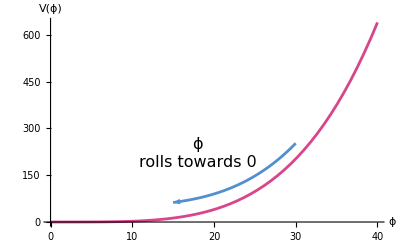

```mathematica
(*Set constants.*)
sm1 = {λ->10^(-3), ϕi->4,ai-> 1, Mpl->1};
(*Plot graph again.*)
p1 = Plot[VQ[x]/.sm1,{x,0,40},PlotStyle->{RGBColor[0.85,0.27,0.54]}, PlotRange->All,AxesLabel->{ϕ,"V(ϕ)"},LabelStyle->{FontSize->16,FontFamily->"Times", ,Black}, Ticks->None];

p2 = Plot[(VQ[ϕ]+50)/.sm1,{ϕ,15,30},PlotStyle->{RGBColor[0.32,0.56,0.81]}, PlotRange->All, Ticks->None]/. Line[x_] :> {Arrowheads[{-.05,0}], Arrow[x]};
t1 = Graphics[Text[Style[OverDot[ϕ,1], 16, FontFamily->"Times"], {18,250}]];
t2 = Graphics[Text[Style["rolls towards 0", 16, FontFamily->"Times"], {18, 190}]];


Show[p1,p2,t1,t2]
```

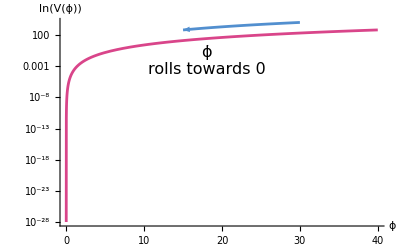

```mathematica
(*Set constants.*)
sm1 = {λ->10^(-3), ϕi->4,ai-> 1, Mpl->1};
(*Plot graph again.*)
p1 = LogPlot[VQ[x]/.sm1,{x,0,40},PlotStyle->{RGBColor[0.85,0.27,0.54]}, PlotRange->All,AxesLabel->{ϕ,"ln(V(ϕ))"},LabelStyle->{FontSize->16,FontFamily->"Times", ,Black}, Ticks->None];

p2 = LogPlot[(VQ[ϕ] 50)/.sm1,{ϕ,15,30},PlotStyle->{RGBColor[0.32,0.56,0.81]}, PlotRange->All, Ticks->None]/. Line[x_] :> {Arrowheads[{-.05,0}], Arrow[x]};
t1 = Graphics[Text[Style[OverDot[ϕ,1], 16, FontFamily->"Times"], {18,-2}]];
t2 = Graphics[Text[Style["rolls towards 0", 16, FontFamily->"Times"], {18, -8}]];


Show[p1,p2,t1,t2]
```

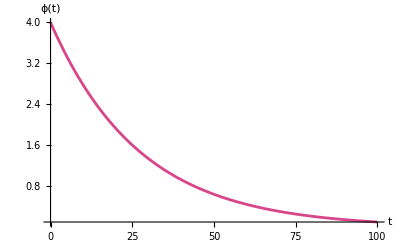

```mathematica
ϕsol[t_]:=ϕ[t]/.sol3[[1]]/.sm1
asol[t_]:=a[t]/.sol3[[1]]/.sm1
Plot[{ϕsol[t]},{t,0,100},PlotRange->All,AxesLabel->{t,"ϕ(t)"}, PlotStyle->{RGBColor[0.85,0.27,0.54]},LabelStyle->{FontSize->16,FontFamily->"Times", ,Black}]
```

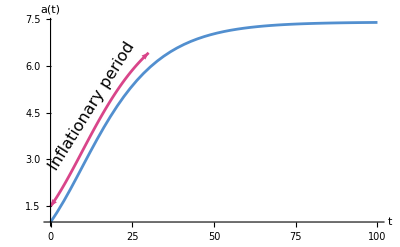

```mathematica
p5 = Plot[asol[t],{t,0,100},PlotRange->All,PlotStyle->{RGBColor[0.32,0.56,0.81]},LabelStyle->{FontSize->16,FontFamily->"Times", Black}, AxesLabel->{t,"a(t)"},FrameTicks->{{#,0.0001 #}&/@FindDivisions[{0.,80000},5]//N,Automatic},Epilog->Text[Rotate[Style["Inflationary period", 16, FontFamily->"Times"],58 Degree],{12.8,4.7}]];

p6=Plot[(asol[t]+0.5)/.sm1,{t,0,30},PlotStyle->{RGBColor[0.85,0.27,0.54]}, PlotRange->All, Ticks->None]/. Line[x_] :> {Arrowheads[{-.05,0.05}], Arrow[x]};
t5 = Graphics[Rotate[Text[Style["Inflationary period", 16, FontFamily->"Times"], {0.5,10}], 50 Degree]];

Show[p5,p6]
```

## Coleman-Weinberg potential

M^4 ((α x^4 log(x/Q))/Q^4+1)

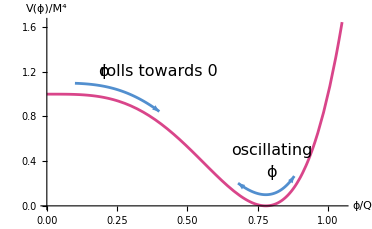

```mathematica
(*Define Coleman-Weinberg potential.*)
VCW[x_]=M^4 (α(x/Q)^4 (Log[x/Q])+1)

(*Set constants.*)
setCons={M->1, α->4 E, Q->1};

p8=Plot[VCW[ϕ]/.setCons,{ϕ,0,1.05},PlotStyle->{RGBColor[0.85,0.27,0.54]}, PlotRange->All,AxesLabel->{ϕ/Q,"V(ϕ)/M^4"},LabelStyle->{FontSize->16,FontFamily->"Times", Black}];

(**)
p9 = Plot[(VCW[ϕ]+0.1)/.setCons,{ϕ,0.1,0.4},PlotStyle->{RGBColor[0.32,0.56,0.81]}, PlotRange->All, Ticks->None]/. Line[x_] :> {Arrowheads[{.05}], Arrow[x]};
p10 = Plot[(VCW[ϕ]+0.1)/.setCons,{ϕ,0.68,0.88},PlotStyle->{RGBColor[0.32,0.56,0.81]}, PlotRange->All, Ticks->None]/. Line[x_] :> {Arrowheads[{-0.05,.05}], Arrow[x]};
t8 = Graphics[Text[Style[OverDot[ϕ,1], 16, FontFamily->"Times"], {0.2,1.2}]];
t9 = Graphics[Text[Style["rolls towards 0", 16, FontFamily->"Times"], {0.4,1.2}]];
t10 = Graphics[Text[Style["oscillating", 16, FontFamily->"Times"], {0.8,0.5}]];
t11=  Graphics[Text[Style[OverDot[ϕ,1], 16, FontFamily->"Times"], {0.8,0.3}]];

Show[p8,p9,p10,t8,t9,t10,t11]
```

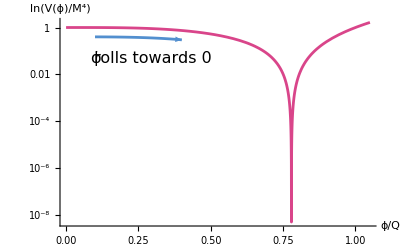

```mathematica
pl8=LogPlot[VCW[ϕ]/.setCons,{ϕ,0,1.05},PlotStyle->{RGBColor[0.85,0.27,0.54]}, PlotRange->All,AxesLabel->{ϕ/Q,"ln(V(ϕ)/M^4)"},LabelStyle->{FontSize->16,FontFamily->"Times", Black}];

pl9 = LogPlot[(VCW[ϕ] 0.4)/.setCons,{ϕ,0.1,0.4},PlotStyle->{RGBColor[0.32,0.56,0.81]}, PlotRange->All, Ticks->None]/. Line[x_] :> {Arrowheads[{.05}], Arrow[x]};
tx8 = Graphics[Text[Style[OverDot[ϕ,1], 16, FontFamily->"Times"], {0.1,-3}]];
tx9 = Graphics[Text[Style["rolls towards 0", 16, FontFamily->"Times"], {0.3,-3}]];


Show[pl8,pl9,tx8,tx9]
```

```mathematica
(*Set constants such that Subscript[M, pl] and m are 1.*)
setCons1 = {G->(1/(8 π)), m->1,M->1, α->4 E, Q->1};

(*Substitute potential into equations of motion.*)
subPot = {V[ϕ[t]]->VCW[ϕ[t]], V'[ϕ[t]]->VCW'[ϕ[t]]};
eq1 = Friedmann1/.subPot/.setCons1
eq2 = continuityEq/.subPot/.setCons1

(*Use NDSolve to obtain numerical solutions for the Friedmann and continuity equations, as they are differential equations..*)
slns = NDSolve[{eq1, eq2, ϕ[0]==4, ϕ'[0]==-0.9, a[0]==1},{ϕ[t],a[t]},{t,0,500}]
```

(3 (a'(t))^2)/(a(t))^2==1/2 ((ϕ'(t))^2+2 (4 ⅇ (ϕ(t))^4 log(ϕ(t))+1))

-(3 a'(t) (ϕ'(t))^2)/(a(t))-ϕ'(t) (ϕ''(t)+4 ⅇ (ϕ(t))^3+16 ⅇ (ϕ(t))^3 log(ϕ(t)))==0

NDSolve::ndsz: At t == 0.0184579, step size is effectively zero; singularity or stiff system suspected.

{{ϕ(t)→InterpolatingFunction[…](t),a(t)→InterpolatingFunction[…](t)},{ϕ(t)→InterpolatingFunction[…](t),a(t)→InterpolatingFunction[…](t)}}

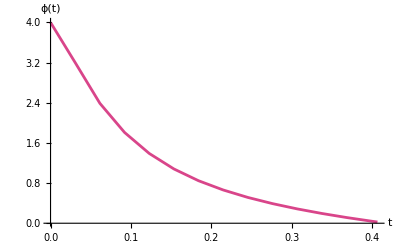

```mathematica
ϕsln[t_]:=ϕ[t]/.slns[[2]]
asln[t_]:=a[t]/.slns[[2]]

(*Plot solutions. Epilog is used to include inset of ϕ(t) for t=0 to t=5.*)
Plot[{ϕsln[t]},{t,0,100},PlotRange->All,AxesLabel->{t,"ϕ(t)"}, PlotStyle->{RGBColor[0.85,0.27,0.54]}, LabelStyle->{FontSize->16,FontFamily->"Times", Black}]
```

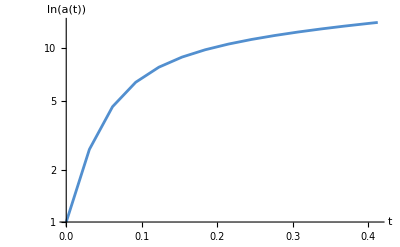

```mathematica
LogPlot[asln[t],{t,0,100},PlotRange->All,PlotStyle->{RGBColor[0.32,0.56,0.81]}, LabelStyle->{FontSize->20,FontFamily->"Times", Black}, AxesLabel->{t,"ln(a(t))"}]
```

```mathematica
Clear[ϕ];
(*Slow-roll conditions break down at ϵ=1 and η=1*)
epsn = Mpl^2/2 (VCW'[ϕ]/VCW[ϕ])^2==1//Simplify
eta = Mpl^2 VCW''[ϕ]/VCW[ϕ]==1

(*Solve ϕ for when conditions break down.*)
ϕend=ϕ/.Solve[{epsn},ϕ][[2]]

(*Solve number of e-folds N before break down for initial ϕ=ϕi*)
Nsol=(1/Mpl^2) Integrate[(VCW[ϕ]/VCW'[ϕ]),{ϕ,ϕend,ϕi}]//Simplify
```

(α^2 Mpl^2 ϕ^6 (4 log(ϕ/Q)+1)^2)/(2 (Q^4+α ϕ^4 log(ϕ/Q))^2)==1

(Mpl^2 ((7 α ϕ^2)/Q^4+(12 α ϕ^2 log(ϕ/Q))/Q^4))/((α ϕ^4 log(ϕ/Q))/Q^4+1)==1

DSolve::argm: DSolve called with 2 arguments; 3 or more arguments are expected.

ReplaceAll::reps: {ϕ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ϕ/.ϕ

$Aborted

```mathematica
(*Applying slow-roll conditions to Friedmann and continuity equations.*)
FEq2 = (a'[t]/a[t])^2==1/(3 Mpl^2) VCW[ϕ[t]]
CEq2 = (3 a'[t] ϕ'[t])/a[t]+(VCW'[ϕ[t]])==0

(*Solve Friedmann and continuity equations to get ϕ[t] and a[t].*)
sol4= DSolve[{FEq2, CEq2, ϕ[0]==ϕi, a[0]==ai},{ϕ[t],a[t]}, t]
```

a'[t]^2/a[t]^2==(M^4 (1+(α Log[ϕ[t]/Q] ϕ[t]^4)/Q^4))/(3 Mpl^2)

M^4 ((α ϕ[t]^3)/Q^4+(4 α Log[ϕ[t]/Q] ϕ[t]^3)/Q^4)+(3 a'[t] ϕ'[t])/a[t]==0

DSolve::bvfail: For some branches of the general solution, unable to solve the conditions.

{}

```mathematica
ϕsol2[t_]:=ϕ[t]/.sol4[[1]]/.setCons
asol2[t_]:=a[t]/.sol4[[1]]/.setCons
Plot[{ϕsol2[t]},{t,0,100},PlotRange->All,AxesLabel->{t,"ϕ(t)"}, PlotStyle->{RGBColor[0.85,0.27,0.54]},LabelStyle->{FontSize->16,FontFamily->"Times", Black}]
```

-Graphics-

## Small field inflation

```mathematica
Clear[VSF]

(*Slow-roll conditions break down at ϵ=1 and η=1*)
epsn1 = Mpl^2/2 (VSF'[ϕ]/VSF[ϕ])^2==1
eta1 = Mpl^2 VSF''[ϕ]/VSF[ϕ]==1

(*Solve ϕ for when conditions break down.*)
ϕend=ϕ/.Solve[epsn1,ϕ][[2]]

(*Solve number of e-folds N before break down for initial ϕ=ϕi*)
Nsol=(1/Mpl^2) Integrate[(VSF[ϕ]/VSF'[ϕ]),{ϕ,ϕend,ϕi}]//Simplify
```

False

False

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ϕ/.{}⟦2⟧

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
Clear[VSF];
VSF[x_]:=M^4 [1-(x/μ) ^p]
setCons4={M->1,Mpl->10^(-3),μ->1,p->4}
(*Applying slow-roll conditions to Friedmann and continuity equations.*)
FEq4 = (a'[t]/a[t])^2==1/(3 Mpl^2) VSF[ϕ[t]];
CEq4 = (3 a'[t] ϕ'[t])/a[t]+(VSF'[ϕ[t]])==0;

(*Solve Friedmann and continuity equations to get ϕ[t] and a[t].*)
sol4 = DSolve[{FEq4, CEq4, ϕ[0]==ϕi, a[0]==ai},{ϕ[t],a[t]}, t]
```

{M→1,Mpl→1,μ→1,p→4}

{{ϕ(t)→ϕi,a(t)→ai ⅇ^(-(t M^(1/2 4(1-(ϕi/μ)^p)))/(√3 Mpl))},{ϕ(t)→ϕi,a(t)→ai ⅇ^((t M^(1/2 4(1-(ϕi/μ)^p)))/(√3 Mpl))}}

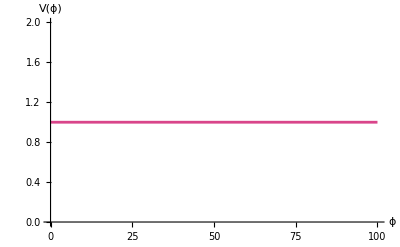

```mathematica
Plot[VSF[ϕ]/.setCons4,{ϕ,0,100},PlotStyle->{RGBColor[0.85,0.27,0.54]}, PlotRange->All,AxesLabel->{ϕ,"V(ϕ)"}, LabelStyle->{FontSize->16, FontFamily->"Times", Black}]
```

{M→1,Mpl→1,μ→4,ϕi→4,ai→1}

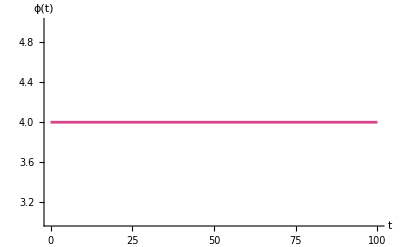

```mathematica
setCons4={M->1,Mpl->1,μ->4,ϕi->4,ai->1}
ϕsol4[t_]:=ϕ[t]/.sol4[[2]]/.setCons4
asol4[t_]:=a[t]/.sol4[[2]]/.setCons4
Plot[{ϕsol4[t]},{t,0,100},PlotRange->All,AxesLabel->{t,"ϕ(t)"}, PlotStyle->{RGBColor[0.85,0.27,0.54]},LabelStyle->{FontSize->16,FontFamily->"Times", Black}]
```

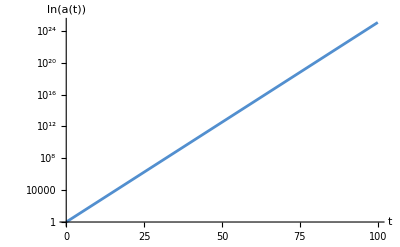

```mathematica
LogPlot[asol4[t],{t,0,100},PlotRange->All,PlotStyle->{RGBColor[0.32,0.56,0.81]},LabelStyle->{FontSize->20,FontFamily->"Times", Black}, AxesLabel->{t,"ln(a(t))"}]
```

## GDWI

```mathematica
VDW[x_]:=M^4 ((x/ϕ0)^2-1)^2

(*Slow-roll conditions break down at ϵ=1 and η=1*)
epsn1 = Mpl^2/2 (VDW'[ϕ]/VDW[ϕ])^2==1;
eta1 = Mpl^2 VDW''[ϕ]/VDW[ϕ]==1;

(*Solve ϕ for when conditions break down.*)
ϕend=ϕ/.Solve[epsn1,ϕ][[2]]

(*Solve number of e-folds N before break down for initial ϕ=ϕi*)
Nsol=(1/Mpl^2) Integrate[(VDW[ϕ]/VDW'[ϕ]),{ϕ,ϕend,ϕi}]//Simplify

setCons4={M->1,Mpl->1,μ->1};
(*Applying slow-roll conditions to Friedmann and continuity equations.*)
FEq4 = (a'[t]/a[t])^2==1/(3 Mpl^2) VDW[ϕ[t]];
CEq4 = (3 a'[t] ϕ'[t])/a[t]+(VDW'[ϕ[t]])==0;

(*Solve Friedmann and continuity equations to get ϕ[t] and a[t].*)
sol4 = DSolve[{FEq4, CEq4, ϕ[0]==ϕi, a[0]==ai},{ϕ[t],a[t]}, t]
```

√(-2 √2 √(Mpl^2 (2 Mpl^2+ϕ0^2))+4 Mpl^2+ϕ0^2)

ConditionalExpression[1/(8 Mpl^2)(2 √2 √(Mpl^2 (2 Mpl^2+ϕ0^2))+ϕ0^2 log(-2 √2 √(Mpl^2 (2 Mpl^2+ϕ0^2))+4 Mpl^2+ϕ0^2)-4 Mpl^2-2 ϕ0^2 log(ϕi)-ϕ0^2+ϕi^2), ]

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is ϕi^2/Mpl^2-Log[ⅇ^(1^2/Mpl^2)] == 0.

DSolve::ifun: Inverse functions are being used by DSolve, so some solutions may not be found.

{{ϕ(t)→ϕi ⅇ^(-(4 M^2 Mpl t)/(√3 ϕ0^2)),a(t)→ai exp((M^2 (-(√3 ϕi^2 ⅇ^(-(8 M^2 Mpl t)/(√3 ϕ0^2)))/(8 M^2 Mpl)-t))/(√3 Mpl)+ϕi^2/(8 Mpl^2))},{ϕ(t)→ϕi ⅇ^((4 M^2 Mpl t)/(√3 ϕ0^2)),a(t)→ai exp((M^2 (t ϕ0^2-(√3 ϕ0^2 ϕi^2 ⅇ^((8 M^2 Mpl t)/(√3 ϕ0^2)))/(8 M^2 Mpl)))/(√3 Mpl ϕ0^2)+ϕi^2/(8 Mpl^2))}}

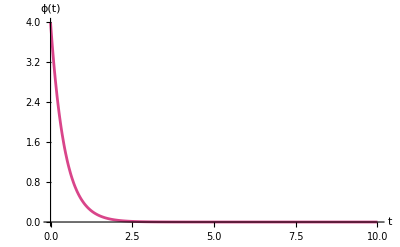

```mathematica
setCons5={M->1,Mpl->1,μ->4,ϕi->4,ai->1,ϕ0->1};
ϕsol5[t_]:=ϕ[t]/.sol4[[1]]/.setCons5
asol5[t_]:=a[t]/.sol4[[1]]/.setCons5
Plot[{ϕsol5[t]},{t,0,10},PlotRange->All,AxesLabel->{t,"ϕ(t)"}, PlotStyle->{RGBColor[0.85,0.27,0.54]},LabelStyle->{FontSize->16,FontFamily->"Times", Black}]
```

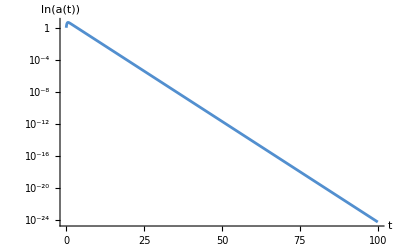

```mathematica
LogPlot[asol5[t],{t,0,100},PlotRange->All,PlotStyle->{RGBColor[0.32,0.56,0.81]},LabelStyle->{FontSize->20,FontFamily->"Times", Black}, AxesLabel->{t,"ln(a(t))"}]
```